0.186191

11.8298

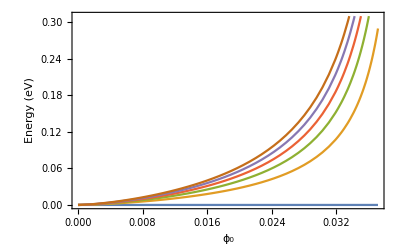

```mathematica
ℏ = 6.582*10^(-16); (*6.52*10^-16 [eV*s]*)
c = 2.998*10^8 ;(*2.998*10^8 [m/s]*)
q = 1.602*10^(-19);(*[C]*)
Subscript[m, e] = 0.51*10^6/c^2; (*0.51 [MeV/c^2]*)
Subscript[v, f] = 10^6; (*10^6 m/s Fermi velocity in graphene [m/s]*)

hw = 191*10^(-3);(*191 [mEv]*)
Emax = 5*10^7; (*[V/m]*)
d = 100*10^(-9);(*[m]*)
K = 2*π/d; (*[m^-1]*)

m = 1*Subscript[m, e];
a = 0.142*10^(-9);(* 142nm lattice constant in graphene [m]*)

phimax = Emax*a/hw;(*unitless*)
Cmax =(1 - (ℏ*Subscript[v, f]*phimax/ (a*hw))^2 )
B = (K/(4*Cmax))*(Subscript[v, f]/hw)^2*(ℏ*phimax/a)^3
w[n_]:=(Subscript[v, f]^2*ℏ^2/((1 - (ℏ*Subscript[v, f]*x/ (a*hw))^2 )*hw))*Sqrt[n*K*x^3 / (2*a^3)]
Plot[{w[0],w[1], w[2],w[3],w[4],w[5]}, {x,0,phimax}, Frame->True,FrameLabel->{"ϕ_0", "Energy (eV)","",""}]
```